FittedModel[87810.6-0.139679 x^2]

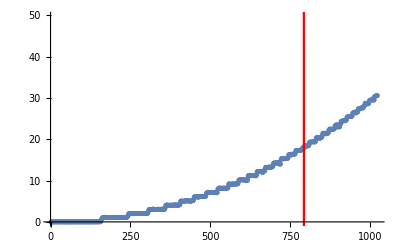

0.00219591

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "unionp"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a+c*x^2,{a,c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
```